## Function

```mathematica
f[{a_,b_}]:=TeXForm@NumberForm[SetAccuracy[a±b,Accuracy@SetPrecision[b,2]],ExponentFunction->(Null&)]//ToString//Quiet
```

```mathematica
f[{1,0.01}]
```

1.000\pm 0.010

## 2.1

```mathematica
V121=7*2
dV121=(0.2*2)
```

14

0.4

```mathematica
V221=3.7
dV221=(0.2*0.5)
```

3.7

0.1

```mathematica
R21=6.85
dR21=0.01*R21+0.1
```

6.85

0.1685

```mathematica
V221/V121*6.85
dRR21=V221/V121*Sqrt[(dV121/V121)^2+(dV221/V221)^2+(dR21/R21)^2]*6.85
```

1.81036

0.0839794

```mathematica
0.7/100*100+0.4
```

1.1

```mathematica
0.7/100*1000+4
```

11.

```mathematica
dRR21=dRR21/Sqrt[2]
```

0.0593824

```mathematica
0.2*250
```

50.

```mathematica
50/Sqrt[2]//N
```

35.3553

```mathematica
f21n1=100
df21n1=1.1
f21n2=1000
df21n2=11
```

100

1.1

1000

11

```mathematica
2Sqrt[f21n1^2 (50*10^(-6))^2 ]//N
```

0.01

```mathematica
2Sqrt[f21n2^2 (50*10^(-6))^2 ]//N
```

0.1

```mathematica
1/Sqrt[(1/0.01^2+ 1/0.1^2)]
```

0.00995037

```mathematica
phaseDifference[t_, dt_, f_, df_]:={2 t f, 2Sqrt[f^2 dt^2 + t^2 df^2]}
```

```mathematica
Rval[Rvor_, dRvor_, Upp1_,dUpp1_, Upp2_,dUpp2_]:= {Rvor * Upp2/Upp1 ,Rvor * Upp2/Upp1 Sqrt[(dUpp1/Upp1)^2 +(dUpp2/Upp2)^2 + (dRvor/Rvor)^2]}
```

## Kapazität

```mathematica
R=226.4;
frequenz={100,500,1000,5000,10000};
UppCh1={1.16,4.0,4.8,4.4,5.2};
UppCh2={190,124,76,17,8.2}/10;
Abstand={2.5,0.5,0.26,0.050,0.025}*10^(-3)
```

{0.0025,0.0005,0.00026,0.00005,0.000025}

```mathematica
dfrequenz=0.7/100*frequenz+{0.4,0.4,4,4,40};
dAbstand=0.2*{1*10^(3) , 250, 100,25,10}*10^(-6);
dAbstand*10^6
dUppch1=0.2*{200*10^(-3),500*10^(-3),1,1,1}
dUppch2=0.2*{5,2,1,0.5,0.2};
dR=0.016*R+0.3
dAbstand=0.2*{1*10^3,250,100,25,10}*10^(-6);
```

{200.,50.,20.,5.,2.}

{0.04,0.1,0.2,0.2,0.2}

3.9224

```mathematica
resistances=Table[Rval[R, dR, UppCh1[[i]], dUppch1[[i]], UppCh2[[i]], dUppch2[[i]]],{i,1,5}]
```

{{3708.28,242.014},{701.84,31.1173},{358.467,18.7255},{87.4727,6.67692},{35.7015,2.3024}}

```mathematica
StringRiffle[f@#&/@Transpose[{UppCh1,dUppch1}], "$ & $"]//CopyToClipboard
StringRiffle[f@#&/@Transpose[{UppCh2,dUppch2}], "$ & $"]//CopyToClipboard
```

```mathematica
Table[phaseDifference[Abstand[[i]],dAbstand[[i]],frequenz[[i]],dfrequenz[[i]]],{i,1,5}]
```

{{0.5,0.0403764},{0.5,0.0501519},{0.52,0.0404069},{0.5,0.0501519},{0.5,0.0403764}}

```mathematica
StringRiffle[f@#&/@Transpose[{Abstand,dAbstand}*10^6], "$ & $"]//CopyToClipboard
```

```mathematica
StringRiffle[f/@resistances, "$ & $"]//CopyToClipboard
```

```mathematica
resistancesPlot=Transpose[{Around[#[[1]],#[[2]]]&/@Transpose[{frequenz,dfrequenz}],Around[#[[1]],#[[2]]]&/@resistances}]
```

{{100.01.1,3708.242.},{500.4.,702.31.},{1000.11.,358.19.},{5000.39.,87.7.},{10000.110.,35.72.3}}

```mathematica
phasedifferences=Table[phaseDifference[Abstand[[i]],dAbstand[[i]], frequenz[[i]], dfrequenz[[i]]],{i,1,5}]
```

{{0.5,0.0403764},{0.5,0.0501519},{0.52,0.0404069},{0.5,0.0501519},{0.5,0.0403764}}

```mathematica
StringRiffle[f/@phasedifferences, "$ & $"]//CopyToClipboard
```

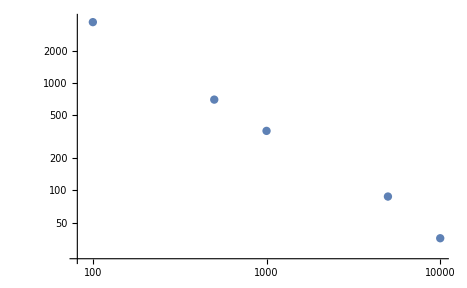

```mathematica
ListLogLogPlot[resistancesPlot]
```

```mathematica
Export[NotebookDirectory[]<>"plt1.pdf",ListLogLogPlot[resistancesPlot,ImageSize->Large,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[15,Black],PlotStyle->Thickness[0.003],FrameLabel->{"f","R_L"},LabelStyle->Directive[Black,15]],Background->None]
```

D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\BNano-MP\B29\plt1.pdf

```mathematica
processed=Table[R*UppCh2[[i]]/(UppCh1[[i]]),{i,1,Length[UppCh2]}]
```

{3708.28,701.84,358.467,87.4727,35.7015}

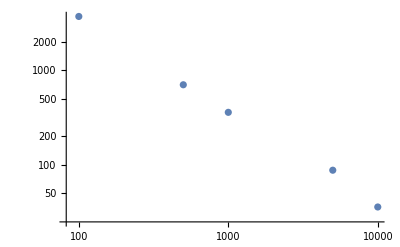

```mathematica
ListLogLogPlot[Transpose[{frequenz,processed}]]
```

```mathematica
FindFit[Transpose[{frequenz,processed}],A x^b,{A,b},x]
```

{A→415376.,b→-1.02469}

```mathematica
Table[Abstand[[i]]*frequenz[[i]]*2,{i,1,Length[frequenz]}]
```

{0.5,0.5,0.52,0.5,0.5}

## Induktivität 2

```mathematica
R=14.8;
Rsp=2.4
frequenz={100,500,1000,5000,10000};
UppCh1={0.46,0.45,0.44,0.4,0.31};
UppCh2={2,9.2,18,84,130.22}/10;
Abstand={2.8,0.475,0.26,0.050,0.024}*10^(-3);
```

2.4

```mathematica
dfrequenz=0.7/100*frequenz+{0.4,0.4,4,4,40};
dAbstand=0.2*{1*10^(3) , 250, 100,25,10}*10^(-6);
dAbstand*10^6
dUppch1=0.2*{100,100,100,50,50}*10^(-3);
dUppch2=0.2*{0.5,2,5,20,20}/10;
dR=0.016*R+0.3
dRsp=0.016*Rsp+0.3
dAbstand=0.2*{1*10^3,250,100,25,10}*10^(-6);
```

{200.,50.,20.,5.,2.}

0.5368

0.3384

```mathematica
resistances=Table[Rval[R, dR, UppCh1[[i]], dUppch1[[i]], UppCh2[[i]], dUppch2[[i]]],{i,1,5}]
```

{{6.43478,0.486066},{30.2578,2.17797},{60.5455,4.86933},{310.8,20.1616},{621.695,35.7119}}

```mathematica
{Rz, dRz}=Transpose[resistances]
```

{{6.43478,30.2578,60.5455,310.8,621.695},{0.486066,2.17797,4.86933,20.1616,35.7119}}

```mathematica
RL=Table[Sqrt[ Rz[[i]]^2 - Rsp^2],{i,1,5}]
```

{5.97046,30.1624,60.4979,310.791,621.691}

```mathematica
dRL=Table[Sqrt[((Rz⟦i⟧^2 dRz⟦i⟧^2)/(Rz⟦i⟧^2-Rsp^2))+((Rsp^2 dRsp^2)/(Rz⟦i⟧^2-Rsp^2))],{i,1,5}]
```

{0.541241,2.18502,4.87317,20.1622,35.7121}

```mathematica
StringRiffle[f@#&/@Transpose[{RL,dRL}], "$ & $"]//CopyToClipboard
```

```mathematica
StringRiffle[f@#&/@Transpose[{UppCh1,dUppch1}], "$ & $"]//CopyToClipboard
```

```mathematica
StringRiffle[f@#&/@Transpose[{UppCh2,dUppch2}], "$ & $"]//CopyToClipboard
```

```mathematica
Table[phaseDifference[Abstand[[i]],dAbstand[[i]],frequenz[[i]],dfrequenz[[i]]],{i,1,5}]
```

{{0.5,0.0403764},{0.5,0.0501519},{0.52,0.0404069},{0.5,0.0501519},{0.5,0.0403764}}

```mathematica
StringRiffle[f@#&/@Transpose[{Abstand,dAbstand}*10^6], "$ & $"]//CopyToClipboard
```

```mathematica
StringRiffle[f/@resistances, "$ & $"]//CopyToClipboard
```

```mathematica
resistancesPlot=Transpose[{Around[#[[1]],#[[2]]]&/@Transpose[{frequenz,dfrequenz}],Around[#[[1]],#[[2]]]&/@Transpose[{RL, dRL}]}]
```

{{100.01.1,6.00.5},{500.4.,30.22.2},{1000.11.,60.5.},{5000.39.,311.20.},{10000.110.,622.36.}}

```mathematica
phasedifferences=Table[phaseDifference[Abstand[[i]],dAbstand[[i]], frequenz[[i]], dfrequenz[[i]]],{i,1,5}]
```

{{0.56,0.0404715},{0.475,0.0501371},{0.52,0.0404069},{0.5,0.0501519},{0.48,0.040347}}

```mathematica
StringRiffle[f/@phasedifferences, "$ & $"]//CopyToClipboard
```

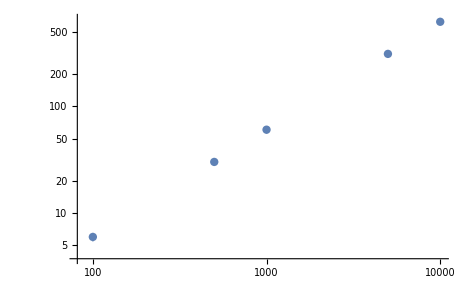

```mathematica
ListLogLogPlot[resistancesPlot]
```

```mathematica
processed=Table[R*UppCh2[[i]]/(UppCh1[[i]]),{i,1,Length[UppCh2]}]
```

{6.43478,30.2578,60.5455,310.8,621.695}

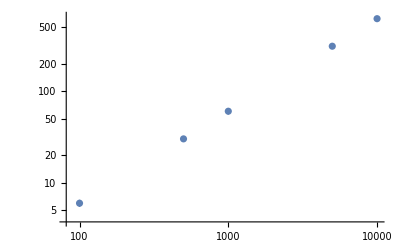

```mathematica
ListLogLogPlot[resistancesPlot]
```

```mathematica
Export[NotebookDirectory[]<>"plt2.pdf",ListLogLogPlot[resistancesPlot,ImageSize->Large,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[15,Black],PlotStyle->Thickness[0.003],FrameLabel->{"f","R_L"},LabelStyle->Directive[Black,15]],Background->None]
```

D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\BNano-MP\B29\plt2.pdf

```mathematica
FindFit[Transpose[{frequenz,RL}],A x^b,{A,b},x]
```

{A→0.0593949,b→1.00501}

```mathematica
Table[Abstand[[i]]*frequenz[[i]]*2,{i,1,Length[frequenz]}]
```

{0.5,0.5,0.52,0.5,0.5}

### Eisenkern

```mathematica
R=14.8;
Rsp=2.4;
dR=0.016*R+0.3
dRsp=0.016*Rsp+0.3
```

0.5368

0.3384

```mathematica
0.2*100*10^(-3)
```

0.02

```mathematica
0.2*2
```

0.4

```mathematica
Rcomp=Rval[R,dR, 0.38,0.02,10.4,0.4]
```

{405.053,30.2162}

```mathematica
RL=Sqrt[Rcomp[[1]]^2 - Rsp^2]
```

405.046

```mathematica
dRL=Sqrt[((Rcomp[[1]]^2Rcomp[[2]]^2)/(Rcomp[[1]]^2-Rsp^2))+((Rsp^2 dRsp^2)/(Rcomp[[1]]^2-Rsp^2))]
```

30.2168

```mathematica
f=1000
df=0.007*f+4
```

1000

11.

```mathematica
RL/(2π f)
```

0.064465

```mathematica
RL/(2π f)Sqrt[(dRL/RL)^2 + (df/f)^2]
```

0.00486115

### Geschl. Eisenkern

```mathematica
R=14.8;
Rsp=2.4;
dR=0.016*R+0.3
dRsp=0.016*Rsp+0.3
```

0.5368

0.3384

```mathematica
0.2*100*10^(-3)
```

0.02

```mathematica
0.2*2
```

0.4

```mathematica
Rcomp=Rval[R,dR, 0.22,0.02,12.8,0.4]
```

{861.091,88.4729}

```mathematica
RL=Sqrt[Rcomp[[1]]^2 - Rsp^2]
```

861.088

```mathematica
dRL=Sqrt[((Rcomp[[1]]^2Rcomp[[2]]^2)/(Rcomp[[1]]^2-Rsp^2))+((Rsp^2 dRsp^2)/(Rcomp[[1]]^2-Rsp^2))]
```

88.4732

```mathematica
f=1000
df=0.007*f+4
```

1000

11.

```mathematica
RL/(2π f)
```

0.137046

```mathematica
RL/(2π f)Sqrt[(dRL/RL)^2 + (df/f)^2]
```

0.0141614

## Induktivität

```mathematica
D[Sqrt[x^2-y^2],x]
D[Sqrt[x^2-y^2],y]
```

x/(√(x^2-y^2))

-y/(√(x^2-y^2))

```mathematica
R=14.8;
Rsp=2.4
frequenz={100,500,1000,5000,10000};
UppCh1={0.46,0.45,0.44,0.4,0.31};
UppCh2={2,9.2,18,84,130.22};
Abstand={2.8,0.475,0.26,0.050,0.024}*10^(-3)
```

2.4

{0.0028,0.000475,0.00026,0.00005,0.000024}

```mathematica
processed=Table[UppCh2[[i]]*R/(UppCh1[[i]]),{i,1,Length[UppCh2]}]
```

{64.3478,302.578,605.455,3108.,6216.95}

```mathematica
2/(0.46/14.8)
```

64.3478

```mathematica
data=Sqrt[#^2-Rsp^2]&/@processed
```

{64.3031,302.568,605.45,3108.,6216.95}

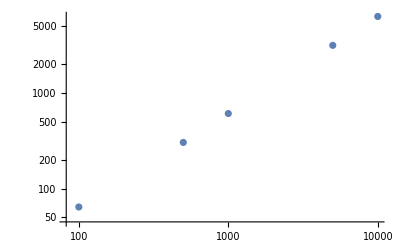

```mathematica
ListLogLogPlot[Transpose[{frequenz,data}]]
```

```mathematica
Table[Abstand[[i]]*frequenz[[i]]*2,{i,1,Length[frequenz]}]
```

{0.56,0.475,0.52,0.5,0.48}

## Induktion

```mathematica
R=14.8
frequenz={100,300,1000,3000,10000}
```

14.8

{100,300,1000,3000,10000}

```mathematica
dfrequenz=0.007*frequenz+{0.4,0.4,4,4,40}
```

{1.1,2.5,11.,25.,110.}

```mathematica
UppR={0.44,0.44,0.44,0.44,0.31}
UppInd={0.042,0.112,0.40,1.2,3.0}
dUppR=0.2*{100,100,100,100,50}*10^(-3)
dUppInd=0.2*{10,20,100,200,500}*10^(-3)
quotient = Table[UppInd[[i]]/UppR[[i]],{i,1,5}]
dquotient = Table[quotient[[i]] * Sqrt[(dUppInd[[i]]/UppInd[[i]])^2 + (dUppR[[i]]/UppR[[i]])^2],{i,1,5}]
```

{0.44,0.44,0.44,0.44,0.31}

{0.042,0.112,0.4,1.2,3.}

{0.02,0.02,0.02,0.02,0.01}

{0.002,0.004,0.02,0.04,0.1}

{0.0954545,0.254545,0.909091,2.72727,9.67742}

{0.00628385,0.0147145,0.06143,0.153728,0.4489}

```mathematica
StringRiffle[f/@Transpose[{frequenz,dfrequenz}],"$ & $"]//CopyToClipboard
```

```mathematica
StringRiffle[f/@Transpose[{UppR,dUppR}],"$ & $"]//CopyToClipboard
```

```mathematica
StringRiffle[f/@Transpose[{UppInd,dUppInd}],"$ & $"]//CopyToClipboard
```

```mathematica
StringRiffle[f/@Transpose[{quotient,dquotient}],"$ & $"]//CopyToClipboard
```

```mathematica
resistancesPlot=Transpose[{Around[#[[1]],#[[2]]]&/@Transpose[{frequenz,dfrequenz}],Around[#[[1]],#[[2]]]&/@Transpose[{quotient,dquotient}]}]
```

{{100.01.1,0.0950.006},{300.02.5,0.2550.015},{1000.11.,0.910.06},{3000.25.,2.730.15},{10000.110.,9.70.4}}

```mathematica
FindFit[Transpose[{frequenz,quotient}],A x^b,{A,b},x]
```

{A→0.000644318,b→1.04412}

```mathematica
Export[NotebookDirectory[]<>"plt3.pdf",ListLogLogPlot[resistancesPlot,ImageSize->Large,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[15,Black],PlotStyle->Thickness[0.003],FrameLabel->{"f (Hz)","(U_(pp, ind))/(U_(pp, R))"},LabelStyle->Directive[Black,15]],Background->None]
```

D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\BNano-MP\B29\plt3.pdf

```mathematica
processed=Table[UppInd[[i]]/UppR[[i]],{i,1,Length[UppInd]}]
```

{0.0954545,0.254545,0.909091,2.72727,9.67742}

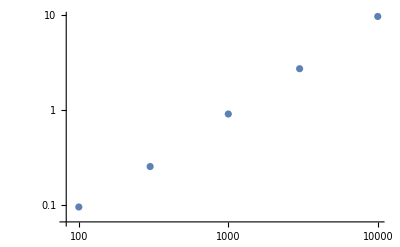

```mathematica
ListLogLogPlot[Transpose[{frequenz,processed}]]
```

```mathematica
FindFit[Transpose[{frequenz,processed}],A x^b,{A,b},x]
```

{A→0.000644318,b→1.04412}

## Steigungen

```mathematica
y2={8,7.5,6}
y1={0.023,0.021,0.017}
x2={9000,8000,6000}
x1={22,23,20}
```

{8,7.5,6}

{0.023,0.021,0.017}

{9000,8000,6000}

{22,23,20}

```mathematica
slst=Table[(Log[y2[[i]]]-Log[y1[[i]]])/(Log[x2[[i]]]-Log[x1[[i]]]),{i,1,3}]
```

{0.973024,1.00452,1.02849}

```mathematica
(slst[[3]]-slst[[1]])/2
```

0.0277348